## Numerical for 3 Flavor Neutrino Oscillation in Matter

### Prep

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/assets

Avogadro number

```mathematica
nAvo=6*10^(23)
```

600000000000000000000000

```mathematica
gF=1.17*10^(-5);
```

### Numerical

```mathematica
numDen[x_]=10^(-12-4.3 x)
```

10^(-12-4.3 x)

```mathematica
theta12=33.36/180*Pi;
theta13=8.66/180*Pi;
theta23=40/180*Pi;
deltacp=0;
(*deltacp=300/180*Pi;*)
m1sq=0.01*10^(-18);
m2sq=m1sq+0.000079*10^(-18);
m3sq=m2sq+0.0027*10^(-18);
rS = 10^(24);
omega=10^(-19);
rSomega=rS*omega;
```

```mathematica
pmns={{Cos[theta12]Cos[theta13],Sin[theta12]Cos[theta13],Sin[theta13]Exp[-I deltacp]},{-Sin[theta12]Cos[theta23]-Cos[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Cos[theta12]Cos[theta23]-Sin[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Sin[theta23]Cos[theta13]},{Sin[theta12]Sin[theta23]-Cos[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],-Cos[theta12]Sin[theta23]-Sin[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],Cos[theta23]Cos[theta13]}}
%//MatrixForm
```

{{0.82571,0.543629,0.150571},{-0.502084,0.586603,0.635459},{0.257129,-0.600304,0.757311}}

(0.82571 | 0.543629 | 0.150571
-0.502084 | 0.586603 | 0.635459
0.257129 | -0.600304 | 0.757311)

```mathematica
hamilV=rSomega pmns.{{m1sq,0,0},{0,m2sq,0},{0,0,m3sq}}.Transpose[pmns];
```

```mathematica
hamilM[x_]=(hamilV+rSomega{{Sqrt[2]gF numDen[x],0,0},{0,0,0},{0,0,0}})*10^(16)//Simplify
```

{{10.0864+16546.3 ⅇ^(-9.90112 x),0.291092,0.291105},{0.291092,11.1494,1.30955},{0.291105,1.30955,11.6223}}

```mathematica
nuF3M[x_]={nuF3Me[x],nuF3Mm[x],nuF3Mt[x]}
```

{nuF3Me[x],nuF3Mm[x],nuF3Mt[x]}

```mathematica
matOsc3 = I nuF3M'[x]==hamilM[x].nuF3M[x]
```

{ⅈ nuF3Me'[x],ⅈ nuF3Mm'[x],ⅈ nuF3Mt'[x]}=={(10.0864+16546.3 ⅇ^(-9.90112 x)) nuF3Me[x]+0.291092 nuF3Mm[x]+0.291105 nuF3Mt[x],0.291092 nuF3Me[x]+11.1494 nuF3Mm[x]+1.30955 nuF3Mt[x],0.291105 nuF3Me[x]+1.30955 nuF3Mm[x]+11.6223 nuF3Mt[x]}

```mathematica
sol3M=NDSolve[matOsc3&&nuF3M[0]=={1,0,0},{nuF3Me,nuF3Mm,nuF3Mt},{x,0,2000}]
```

{{nuF3Me→InterpolatingFunction[{{0., 2000.}}, <>],nuF3Mm→InterpolatingFunction[{{0., 2000.}}, <>],nuF3Mt→InterpolatingFunction[{{0., 2000.}}, <>]}}

```mathematica
probesqrt=nuF3Me/.sol3M[[1]]
probmsqrt=nuF3Mm/.sol3M[[1]]
probtsqrt=nuF3Mt/.sol3M[[1]]
```

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

```mathematica
norm[x_]=Abs[probesqrt[x]]^2+Abs[probmsqrt[x]]^2+Abs[probtsqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2

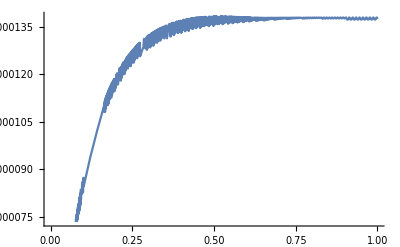

```mathematica
Plot[norm[x],{x,0,1}]
```

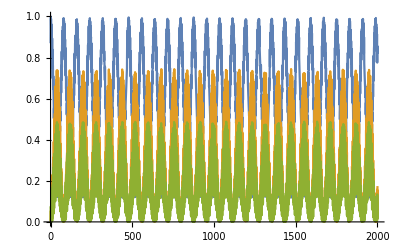

```mathematica
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probmsqrt[x]]^2/norm[x],Abs[probtsqrt[x]]^2/norm[x]},{x,0,2000}]
```

```mathematica
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probtsqrt[x]]^2/norm[x]},{x,0,1}]
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probmsqrt[x]]^2/norm[x]},{x,0,1}]
```